## Computations supporting Example 4.6 in the paper ‘The truncated univariate rational moment problem’ by Rajkamal Nailwal and Aljaž Zalar.

### Let K=(-infty,0]\cup [1,2]\cup [3,\infty). Then the natural description S is {x(x-1),(x-2)(x-3)} and S^π={1,x(x-1),(x-2)(x-3),x(x-1)(x-2)(x-3)}. We will generate a moment sequence {γ_i}_{i=0,...,6} such that there does not exist γ_7,γ_8 such that the moment matrix H_1 would be positive semidefinite and singular, and all other localizing matrices H_f when f runs over S^π would be positive definite. Hence, there is no minimal (i.e., having the smallest number of atoms in the support) representing measure avoiding all boundary points of K. However, there are γ_7,γ_8,γ_9,γ_10 such that the statement above is true. Hence, a K-representing measure with 0 densities in all boundary points for γ exists. A minimal such measure contains 5 atoms. We generate a sequence {γ_i}_i of degree 6 using 6 atoms x1=0, x2=1, x3=2, x4=3,x5=-1,x6=-2 all with densities 1/6, i.e., γ_i=∑_{j=1}^6 1/6*x_j^i for i=0,...,6.

```mathematica
atoms={0,1,2,3,-1,3/2};
```

```mathematica
gamma={1};
For[i=1,i<7,i++,moment=0;For[j=1,j<7,j++,moment=moment+1/6*atoms[[j]]^i];AppendTo[gamma,moment]]
gamma
```

{1,13/12,23/8,307/48,555/32,9043/192,17203/128}

### Let us compute the polynomials needed to generate a rational sequence γ^{(0)}_0, γ^{(1)}_1,γ^{(1)}_2,γ^{(2)}_1,γ^{(2)}_2,γ^{(3)}_1,γ^{(3)}_2 with the notation as in Remark 1.1 of the paper. The real poles are λ_1=0,λ_2=1,λ_3=2.

```mathematica
Expand[x(x-1)^2(x-2)^2]
Expand[x^2(x-1)(x-2)^2]
Expand[x^2(x-2)^2]
Expand[x^2(x-1)^2(x-2)]
Expand[x^2(x-1)^2]
```

4 x-12 x^2+13 x^3-6 x^4+x^5

-4 x^2+8 x^3-5 x^4+x^5

4 x^2-4 x^3+x^4

-2 x^2+5 x^3-4 x^4+x^5

x^2-2 x^3+x^4

### The rational moments are: a := γ_ 0^{(0)} = L (x^2*(x-1)^2*(x-2)^2) = L (x.08^6 - 6 x^5 + 13 x^4 - 12x^3+4x^2), b1 := γ_ 1^{(1)} = L (x *(x-1)^2*(x-2)^2) = L (x.08^5 - 6 x^4 + 13 x^3 - 12x^2+4x), b2 := γ_ 1^{(2)} = L ((x-1)^2*(x-2)^2) = L (x.08^4 - 6 x^3 + 13 x^2 - 12x+4), c1 := γ_ 2^{(1)} = L (x^2*(x-1)*(x - 2)^2) = L (x^5-5x^4+8x^3-4x^2), c2 := γ_ 2^{(2)} = L (x^2*(x - 2)^2) = L (x^4-4x^3+4x^2), d1 := γ_ 3^{(1)} = L (x^2*(x-1)*^2*(x - 2)) = L (x^5-4x^4+5x^3-2x^2), d2 := γ_ 3^{(2)} = L (x^2*(x - 1)^2) = L (x^4-2x^3+x^2),

```mathematica
a=gamma[[7]]-6*gamma[[6]]+13*gamma[[5]]-12*gamma[[4]]+4*gamma[[3]]
b1=gamma[[6]]-6*gamma[[5]]+13*gamma[[4]]-12*gamma[[3]]+4*gamma[[2]]
b2=gamma[[5]]-6*gamma[[4]]+13*gamma[[3]]-12*gamma[[2]]+4*gamma[[1]]
c1=gamma[[6]]-5*gamma[[5]]+8*gamma[[4]]-4*gamma[[3]]
c2=gamma[[5]]-4*gamma[[4]]+4*gamma[[3]]
d1=gamma[[6]]-4*gamma[[5]]+5*gamma[[4]]-2*gamma[[3]]
d2=gamma[[5]]-2*gamma[[4]]+gamma[[3]]
```

1539/128

-255/64

235/32

3/64

313/96

253/64

713/96

### Let us expand the localizing polynomials f1=x(x-1), f2=(x-2)(x-3), f3=f1*f2.

```mathematica
Expand[x(x-1)]
Expand[(x-2)(x-3)]
Expand[x(x-1)(x-2)(x-3)]
```

-x+x^2

6-5 x+x^2

-6 x+11 x^2-6 x^3+x^4

### Let us compute the localizing matrices H1=H_1, H2=H_{f1}, H3=H_{f2}, H4=H_{f3}. For H4 we will need: m0:=L_{f3}(1)=γ4-6*γ3+11*γ2-6*γ1, m1:=L_{f3}(x)=γ5-6*γ4+11*γ3-6*γ2, m2:=L_{f3}(x^2)=γ6-6*γ5+11*γ4-6*γ3.

```mathematica
H1=HankelMatrix[gamma[[1;;4]],gamma[[4;;7]]];
MatrixForm[H1]
H2=H1[[2;;4,2;;4]]-H1[[1;;3,2;;4]];
MatrixForm[H2]
H3=H1[[2;;4,2;;4]]-5*H1[[1;;3,2;;4]]+6*H1[[1;;3,1;;3]];
MatrixForm[H3]
m0=gamma[[5]]-6*gamma[[4]]+11gamma[[3]]-6*gamma[[2]];
m1=gamma[[6]]-6*gamma[[5]]+11gamma[[4]]-6*gamma[[3]];
m2=gamma[[7]]-6*gamma[[6]]+11gamma[[5]]-6*gamma[[4]];
H4={{m0,m1},{m1,m2}};
MatrixForm[H4]
```

(1 | 13/12 | 23/8 | 307/48
13/12 | 23/8 | 307/48 | 555/32
23/8 | 307/48 | 555/32 | 9043/192
307/48 | 555/32 | 9043/192 | 17203/128)

(43/24 | 169/48 | 1051/96
169/48 | 1051/96 | 5713/192
1051/96 | 5713/192 | 33523/384)

(83/24 | -71/48 | 251/96
-71/48 | 251/96 | -239/192
251/96 | -239/192 | 1139/384)

(131/32 | -247/64
-247/64 | 539/128)

### Let us check H1,H2,H3,H4 are indeed positive semidefinite.

```mathematica
N[Eigenvalues[H1]]
N[Eigenvalues[H2]]
N[Eigenvalues[H3]]
N[Eigenvalues[H4]]
```

{153.595,1.4378,0.46075,0.123526}

{98.8874,0.845656,0.306055}

{6.7426,1.71464,0.581825}

{8.01216,0.292524}

### Let us determine possible γ_{7}, γ_{8}. Since there is no polynomial of odd degree in S^π, we do not have any restriction on the value γ_{7}. We denote γ_{7},γ_{8} with variables x, y, respectively.

### Possible extensions of H1. Since the Schur complement of H1 (Schur1) in the extension must be positive semidefinite, this gives as a lower bound of γ_{8}. So γ_{8}≥0 and Schur1>=0. The form of the extension is the following:

```mathematica
H1temp=IdentityMatrix[5];
H1temp[[1;;4,1;;4]]=H1;
H1temp[[1;;3,{5}]]={{gamma[[5]]},{gamma[[6]]},{gamma[[7]]}};
H1temp[[{5},1;;3]]=Transpose[{{gamma[[5]]},{gamma[[6]]},{gamma[[7]]}}];
H1temp;
extH1[x_,y_]={{1,13/12,23/8,307/48,555/32},{13/12,23/8,307/48,555/32,9043/192},{23/8,307/48,555/32,9043/192,17203/128},{307/48,555/32,9043/192,17203/128,x},{555/32,9043/192,17203/128,x,y}};
MatrixForm[extH1[x,y]]
```

(1 | 13/12 | 23/8 | 307/48 | 555/32
13/12 | 23/8 | 307/48 | 555/32 | 9043/192
23/8 | 307/48 | 555/32 | 9043/192 | 17203/128
307/48 | 555/32 | 9043/192 | 17203/128 | x
555/32 | 9043/192 | 17203/128 | x | y)

### So Schur1[x,y] is the following:

```mathematica
Schur1[x_]=Simplify[extH1[x,y][[5,1;;4]].Inverse[H1].extH1[x,y][[1;;4,5]]]
Schur1[x_,y_]=Simplify[y-Schur1[x]]
TeXForm[Schur1[x,y]]
```

(4733803996639-24532643328 x+32440320 x^2)/87146496

-4733803996639/87146496+(15971773 x)/56736-(220 x^2)/591+y

-\frac{220 x^2}{591}+\frac{15971773 x}{56736}+y-\frac{4733803996639}{87146496}

### Hence, y≥Schur1[x].

### Possible extensions of H2. Since the Schur complement of H2 (Schur2) in the extension must be positive semidefinite, this gives as a lower bound of γ_{8}. So γ_{8}-γ_{7}≥0 and Schur2≥0. The form of the extension is the following:

```mathematica
H2temp=IdentityMatrix[4];
H2temp[[1;;3,1;;3]]=H2;
H2temp[[1;;2,{4}]]={{gamma[[6]]-gamma[[5]]},{gamma[[7]]-gamma[[6]]}};
H2temp[[{4},1;;2]]=Transpose[{{gamma[[6]]-gamma[[5]]},{gamma[[7]]-gamma[[6]]}}];
H2temp;
extH2[x_,y_]={{43/24,169/48,1051/96,5713/192},{169/48,1051/96,5713/192,33523/384},{1051/96,5713/192,33523/384,x-gamma[[7]]},{5713/192,33523/384,x-gamma[[7]],y-x}};
MatrixForm[extH2[x,y]]
```

(43/24 | 169/48 | 1051/96 | 5713/192
169/48 | 1051/96 | 5713/192 | 33523/384
1051/96 | 5713/192 | 33523/384 | -17203/128+x
5713/192 | 33523/384 | -17203/128+x | -x+y)

(43/24 | 169/48 | 1051/96 | 5713/192
169/48 | 1051/96 | 5713/192 | 33523/384
1051/96 | 5713/192 | 33523/384 | -17203/128+x
5713/192 | 33523/384 | -17203/128+x | -x+y)

### So Schur2[x,y] is the following:

```mathematica
Schur2[x_]=Simplify[extH2[x,y][[4,1;;3]].Inverse[H2].extH2[x,y][[1;;3,4]]]
Schur2[x_,y_]=Simplify[y-x-Schur2[x]]
TeXForm[Schur2[x,y]]
```

6505636110821/161021952-(3169529 x)/14976+(11 x^2)/39

-6505636110821/161021952+(3154553 x)/14976-(11 x^2)/39+y

-\frac{11 x^2}{39}+\frac{3154553 x}{14976}+y-\frac{6505636110821}{161021952}

### Hence, y-x≥Schur2[x]. Equivalently, y≥Schur2[x]+x.

### Possible extensions of H3. Since the Schur complement of H3 (Schur3) in the extension must be positive semidefinite, this gives as a lower bound of γ_{8}. So γ_{8}-5*γ_{7}+6*γ_{6}≥0 and Schur3≥0. The form of the extension is the following:

```mathematica
H3temp=IdentityMatrix[4];
H3temp[[1;;3,1;;3]]=H3;
H3temp[[1;;2,{4}]]={{gamma[[6]]-5*gamma[[5]]+6*gamma[[4]]},{gamma[[7]]-5*gamma[[6]]+6*gamma[[5]]}};
H3temp[[{4},1;;2]]=Transpose[{{gamma[[6]]-5*gamma[[5]]+6*gamma[[4]]},{gamma[[7]]-5*gamma[[6]]+6*gamma[[5]]}}];
H3temp;
extH3[x_,y_]={{83/24,-71/48,251/96,-239/192},{-71/48,251/96,-239/192,1139/384},{251/96,-239/192,1139/384,x-5*gamma[[7]]+6*gamma[[6]]},{-239/192,1139/384,x-5*gamma[[7]]+6*gamma[[6]],y-5*x+6*gamma[[7]]}};
MatrixForm[extH3[x,y]]
```

(83/24 | -71/48 | 251/96 | -239/192
-71/48 | 251/96 | -239/192 | 1139/384
251/96 | -239/192 | 1139/384 | -49843/128+x
-239/192 | 1139/384 | -49843/128+x | 51609/64-5 x+y)

### So Schur3[x,y] is the following:

```mathematica
Schur3[x_]=Simplify[extH3[x,y][[4,1;;3]].Inverse[H3].extH3[x,y][[1;;3,4]]]
Schur3[x_,y_]=Simplify[extH3[x,y][[4,4]]-Schur3[x]]
TeXForm[Schur3[x,y]]
```

29259527430545/190439424-(14016149 x)/17712+(376 x^2)/369

-29105958864401/190439424+(13927589 x)/17712-(376 x^2)/369+y

-\frac{376 x^2}{369}+\frac{13927589 x}{17712}+y-\frac{29105958864401}{190439424}

### Hence, y-5*x+6*γ_{2k}≥Schur3[x]. Equivalently, y≥Schur3[x]+5*x-6*γ_{2k}.

### Possible extensions of H4. Since the Schur complement of H4 (Schur4) in the extension must be positive semidefinite, this gives as a lower bound of γ_{2 k + 2}. So γ_{2k+2}-6*γ_{2k+1}+11*γ_{2k}-6*γ_{2k-1}≥0 and Schur4≥0. The form of the extension is the following:

```mathematica
H4temp=IdentityMatrix[3];
H4temp[[1;;2,1;;2]]=H4;
H4temp[[1,3]]=gamma[[7]]-6*gamma[[6]]+11*gamma[[5]]-6*gamma[[4]];
H4temp[[3,1]]=gamma[[7]]-6*gamma[[6]]+11*gamma[[5]]-6*gamma[[4]];
H4temp;
extH4[x_,y_]={{131/32,-247/64,539/128},{-247/64,539/128,x-6*gamma[[7]]+11*gamma[[6]]-6*gamma[[5]]},{539/128,x-6*gamma[[7]]+11*gamma[[6]]-6*gamma[[5]],y-6*x+11*gamma[[7]]-6*gamma[[6]]}};
MatrixForm[extH4[x,y]]
```

(131/32 | -247/64 | 539/128
-247/64 | 539/128 | -37667/96+x
539/128 | -37667/96+x | 153061/128-6 x+y)

### So Schur4[x,y] is the following:

```mathematica
Schur4[x_]=Simplify[extH4[x,y][[3,1;;2]].Inverse[H4].extH4[x,y][[1;;2,3]]]
Schur4[x_,y_]=Simplify[extH4[x,y][[3,3]]-Schur4[x]]
TeXForm[Schur4[x,y]]
```

11655946144619/44236800-(39075617 x)/28800+(131 x^2)/75

-11603048263019/44236800+(38902817 x)/28800-(131 x^2)/75+y

-\frac{131 x^2}{75}+\frac{38902817 x}{28800}+y-\frac{11603048263019}{44236800}

### Hence, y-6*x+11*γ_{2k}-6γ_{2k-1}≥Schur4[x]. Equivalently, y≥Schur4[x]+6*x-11*γ_{2k}+6*γ_{2k-1}.

### Now we plot all lower bounds on y as functions of x and see which one bounds y from below the most.

```mathematica
lower1[x_]=Max[Schur1[x],0];
lower2[x_]=Max[Schur2[x]+x,x];
lower3[x_]=Max[Schur3[x]+5x-6*gamma[[7]],5x-6*gamma[[7]]];
lower4[x_]=Max[Schur4[x]+6x-11*gamma[[7]]+6*gamma[[6]],6x-11*gamma[[7]]+6*gamma[[6]]];
```

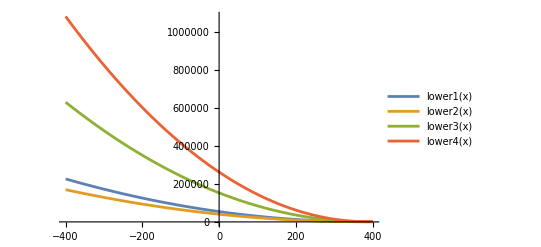

```mathematica
Plot[{lower1[x],lower2[x],lower3[x],lower4[x]},{x,-400,400},PlotLegends->"Expressions"]
```

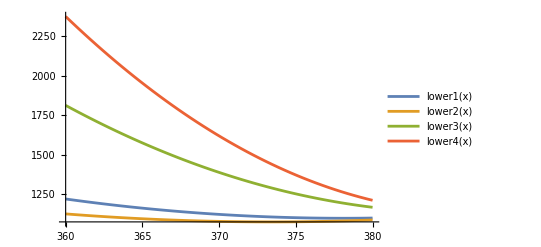

```mathematica
Plot[{lower1[x],lower2[x],lower3[x],lower4[x]},{x,360,380},PlotLegends->"Expressions"]
```

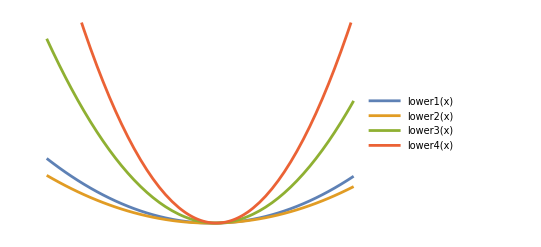

```mathematica
Plot[{lower1[x],lower2[x],lower3[x],lower4[x]},{x,0,700},PlotLegends->Placed["Expressions",{0.75,0.75}],Axes->False]
```

```mathematica
N[Reduce[lower1[x]>=lower2[x]&&lower1[x]>=lower3[x]&&lower1[x]>=lower4[x],x]]
```

False

### We see that lower1 is never the most limiting localizing matrix. Hence, for each γ_{7} and for the smallest possible γ_{8} making all extensions of the localizing Hankel matrices positive semidefinite, H_1 will be positive definite. Hence, in every minimal measure at least one of the boundary points {0,1,2} of K will be an atom.

### Let us now choose γ_{7}=370, γ_{8}=2000 all localizing matrices are psd.

```mathematica
x=370;y=2000;
AppendTo[gamma,x];
AppendTo[gamma,y]
```

{1,13/12,23/8,307/48,555/32,9043/192,17203/128,370,2000}

### In what follows we will denote possible γ_{9}, γ_{10} with z,w.

### Possible extensions of H1. Since the Schur complement of H1 (Schur1s2(H1)) in the extension must be positive semidefinite, this gives as a lower bound of γ_{10}. So γ_{10}≥0 and Schur1s2(H1)≥0. The form of the extension is the following:

```mathematica
H1temp=IdentityMatrix[6];
H1temp[[1;;5,1;;5]]=extH1[x,y];
H1temp[[1;;4,{6}]]={{gamma[[6]]},{gamma[[7]]},{gamma[[8]]},{gamma[[9]]}};
H1temp[[{6},1;;4]]=Transpose[{{gamma[[6]]},{gamma[[7]]},{gamma[[8]]},{gamma[[9]]}}];
H1temp;
extH1s2[z_,w_]={{1,13/12,23/8,307/48,555/32,9043/192},{13/12,23/8,307/48,555/32,9043/192,17203/128},{23/8,307/48,555/32,9043/192,17203/128,370},{307/48,555/32,9043/192,17203/128,370,2000},{555/32,9043/192,17203/128,370,2000,z},{9043/192,17203/128,370,2000,z,w}};
MatrixForm[extH1s2[z,w]]
```

(1 | 13/12 | 23/8 | 307/48 | 555/32 | 9043/192
13/12 | 23/8 | 307/48 | 555/32 | 9043/192 | 17203/128
23/8 | 307/48 | 555/32 | 9043/192 | 17203/128 | 370
307/48 | 555/32 | 9043/192 | 17203/128 | 370 | 2000
555/32 | 9043/192 | 17203/128 | 370 | 2000 | z
9043/192 | 17203/128 | 370 | 2000 | z | w)

### So Schur1s2(H1) is the following:

```mathematica
Schur1s2[z_]=Simplify[extH1s2[z,w][[6,1;;5]].Inverse[extH1s2[z,w][[1;;5,1;;5]]].extH1s2[z,w][[1;;5,6]]]
Schur1s2[z_,w_]=Simplify[extH1s2[z,w][[6,6]]-Schur1s2[z]]
```

(192973422961933491064291-145030264320098304 z+629663411994624 z^2)/552646466862465024

w+(-192973422961933491064291+145030264320098304 z-629663411994624 z^2)/552646466862465024

### Hence, w≥Schur1s2[z].

### Possible extensions of H2. Since the Schur complement of H2 (Schur2s2) in the extension must be positive semidefinite, this gives as a lower bound of γ_{10}. So γ_{10}-γ_{9}≥0 and Schur2s2≥0. The form of the extension is the following:

```mathematica
H2temp=IdentityMatrix[5];
H2temp[[1;;4,1;;4]]=extH2[x,y];
H2temp[[1;;3,{5}]]={{gamma[[7]]-gamma[[6]]},{gamma[[8]]-gamma[[7]]},{gamma[[9]]-gamma[[8]]}};
H2temp[[{5},1;;3]]=Transpose[{{gamma[[7]]-gamma[[6]]},{gamma[[8]]-gamma[[7]]},{gamma[[9]]-gamma[[8]]}}];
H2temp;
extH2s2[z_,w_]={{43/24,169/48,1051/96,5713/192,33523/384},{169/48,1051/96,5713/192,33523/384,30157/128},{1051/96,5713/192,33523/384,30157/128,1630},{5713/192,33523/384,30157/128,1630,z-gamma[[9]]},{33523/384,30157/128,1630,z-gamma[[9]],w-z}};
MatrixForm[extH2s2[z,w]]
```

(43/24 | 169/48 | 1051/96 | 5713/192 | 33523/384
169/48 | 1051/96 | 5713/192 | 33523/384 | 30157/128
1051/96 | 5713/192 | 33523/384 | 30157/128 | 1630
5713/192 | 33523/384 | 30157/128 | 1630 | -2000+z
33523/384 | 30157/128 | 1630 | -2000+z | w-z)

### So the Schur2s2 is the following:

```mathematica
Schur2s2[z_]=Simplify[extH2s2[z,w][[5,1;;4]].Inverse[extH2s2[z,w][[1;;4,1;;4]]].extH2s2[z,w][[1;;4,5]]]
Schur2s2[z_,w_]=Simplify[extH2s2[z,w][[5,5]]-Schur2s2[z]]
```

(54180627497473162289645-1067230319927132160 z+213692876587008 z^2)/197028480362397696

w+(-54180627497473162289645+870201839564734464 z-213692876587008 z^2)/197028480362397696

### Hence, w-z≥Schur2s2[z]. Equivalently, w≥Schur2s2[z]+z.

### Possible extensions of H3. Since the Schur complement of H3 (Schur3s2) in the extension must be positive semidefinite, this gives as a lower bound of γ_{2 k + 4}. So γ_{2k+4}-5*γ_{2k+3}+6*γ_{2k+2}≥0 and Schur3s2≥0. The form of the extension is the following:

```mathematica
H3temp=IdentityMatrix[5];
H3temp[[1;;4,1;;4]]=extH3[x,y];
H3temp[[1;;3,{5}]]={{gamma[[7]]-5*gamma[[6]]+6*gamma[[5]]},{gamma[[8]]-5*gamma[[7]]+6*gamma[[6]]},{gamma[[9]]-5*gamma[[8]]+6*gamma[[7]]}};
H3temp[[{5},1;;3]]=Transpose[{{gamma[[7]]-5*gamma[[6]]+6*gamma[[5]]},{gamma[[8]]-5*gamma[[7]]+6*gamma[[6]]},{gamma[[9]]-5*gamma[[8]]+6*gamma[[7]]}}];
H3temp;
extH3s2[z_,w_]={{83/24,-71/48,251/96,-239/192,1139/384},{-71/48,251/96,-239/192,1139/384,-2483/128},{251/96,-239/192,1139/384,-2483/128,61209/64},{-239/192,1139/384,-2483/128,61209/64,z-5*gamma[[9]]+6*gamma[[8]]},{1139/384,-2483/128,61209/64,z-5*gamma[[9]]+6*gamma[[8]],w-5*z+6*gamma[[9]]}};
MatrixForm[extH3s2[z,w]]
```

(83/24 | -71/48 | 251/96 | -239/192 | 1139/384
-71/48 | 251/96 | -239/192 | 1139/384 | -2483/128
251/96 | -239/192 | 1139/384 | -2483/128 | 61209/64
-239/192 | 1139/384 | -2483/128 | 61209/64 | -7780+z
1139/384 | -2483/128 | 61209/64 | -7780+z | 12000+w-5 z)

### So Schur3s2 is the following:

```mathematica
Schur3s2[z_]=Simplify[extH3s2[z,w][[5,1;;4]].Inverse[extH3s2[x,y][[1;;4,1;;4]]].extH3s2[z,w][[1;;4,5]]]
Schur3s2[z_,w_]=Simplify[extH3s2[z,w][[5,5]]-Schur3s2[z]]
```

(37429234824369166500205+1125036862009933824 z+56162871410688 z^2)/34351262630903808

w+(-37017019672798320804205-1296793175164452864 z-56162871410688 z^2)/34351262630903808

### Hence, w-5*z+6*γ_{2k+2}≥Schur3s2[z]. Equivalently, w≥Schur3s2[z]+5*z-6*γ_{2k+2}.

### Possible extensions of H4. Since the Schur complement of H4 (Schur4s2) in the extension must be positive semidefinite, this gives as a lower bound of γ_{2 k + 4}. So γ_{2k+4}-6*γ_{2k+3}+11*γ_{2k+2}-6*γ_{2k+1}≥0 and Schur4s2≥0. The form of the extension is the following:

```mathematica
H4temp=IdentityMatrix[4];
H4temp[[1;;3,1;;3]]=extH4[x,y];
H4temp[[{1,2},{4}]]={{gamma[[8]]-6*gamma[[7]]+11*gamma[[6]]-6*gamma[[5]]},{gamma[[9]]-6*gamma[[8]]+11*gamma[[7]]-6*gamma[[6]]}};
H4temp[[{4},{1,2}]]=Transpose[{{gamma[[8]]-6*gamma[[7]]+11*gamma[[6]]-6*gamma[[5]]},{gamma[[9]]-6*gamma[[8]]+11*gamma[[7]]-6*gamma[[6]]}}];
H4temp;
extH4s2[z_,w_]=
{{131/32,-247/64,539/128,-2147/96},{-247/64,539/128,-2147/96,124901/128},{539/128,-2147/96,124901/128,z-6*gamma[[9]]+11*gamma[[8]]-6*gamma[[7]]},{-2147/96,124901/128,z-6*gamma[[9]]+11*gamma[[8]]-6*gamma[[7]],w-6*z+11*gamma[[9]]-6*gamma[[8]]}};
MatrixForm[extH4s2[z,w]]
```

(131/32 | -247/64 | 539/128 | -2147/96
-247/64 | 539/128 | -2147/96 | 124901/128
539/128 | -2147/96 | 124901/128 | -559129/64+z
-2147/96 | 124901/128 | -559129/64+z | 19780+w-6 z)

### So Schur4s2 is the following:

```mathematica
Schur4s2[z_]=Simplify[extH4s2[z,w][[4,1;;3]].Inverse[extH4s2[z,w][[1;;3,1;;3]]].extH4s2[z,w][[1;;3,4]]]
Schur4s2[z_,w_]=Simplify[extH4s2[z,w][[4,4]]-Schur4s2[z]]
```

(55445206736584889651+2238276391948800 z+50960793600 z^2)/19387769265792

w+(-55061716660507523891-2354603007543552 z-50960793600 z^2)/19387769265792

### Hence, w-6*z+11*γ_{2k+2}-6γ_{2k+1}≥Schur4s2[z]. Equivalently, w≥Schur4s2[z]+6*z-11*γ_{2k+2}+6*γ_{2k+1}.

### Now we plot all lower bounds on w as functions of z and see which one bounds w from below the most.

```mathematica
lower1s2[z_]=Max[Schur1s2[z],0];
lower2s2[z_]=Max[Schur2s2[z]+z,z];
lower3s2[z_]=Max[Schur3[z]+5z-6*gamma[[9]],5z-6*gamma[[9]]];
lower4s2[z_]=Max[Schur4[z]+6z-11*gamma[[9]]+6*gamma[[8]],6z-11*gamma[[9]]+6*gamma[[8]]];
```

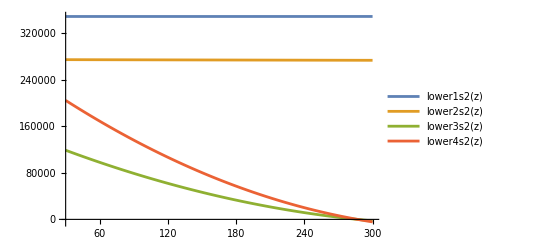

```mathematica
Plot[{lower1s2[z],lower2s2[z],lower3s2[z],lower4s2[z]},{z,30,300},PlotLegends->"Expressions"]
```

```mathematica
N[Reduce[lower1s2[z]>lower2s2[z]&&lower1s2[z]>lower3s2[z]&&lower1s2[z]>lower4s2[z],z]]
```

-71.4902<z<845.199

### We see that for z on the interval -71.4902<z<845.199, H_1 is the most restrictive Hankel matrix. Hence choosing the smallest possible γ_{10} for γ_{9} from this intervals gives us a representing measure avoiding boundary points of K. We just avoid at most 3 forbidden values of γ_{9} such that one of λ_i is an atom in the representing measure.